```mathematica
<<"/Users/lucaarnaboldi/Desktop/staircase-ss/mathematica/CommitteeIsserlis.m"
```

```mathematica
Omega
```

{{ω[1,1],ω[1,2],ω[1,3],ω[1,4],0},{ω[1,2],ω[2,2],ω[2,3],ω[2,4],0},{ω[1,3],ω[2,3],ω[3,3],ω[3,4],0},{ω[1,4],ω[2,4],ω[3,4],ω[4,4],0},{0,0,0,0,Δ}}

```mathematica
I2noise = Expand[(3*lfs[1]^2-3)*(3*lfs[2]^2-3)]
(**)
(*I2 = Expand[(lfs[1])*(lfs[2])]*)
(*I2 = Expand[(lfs[1]^2-1)*(lfs[2]^2-1)]*)
(*I2 = Expand[(lfs[1]^3-3*lfs[1])*(lfs[2]^3-3*lfs[2])]*)
I2=Expand[(lfs[1]^4-6*lfs[1]^2+3)*(lfs[2]^4-6*lfs[2]^2+3)]
(**)
(*I3 = Expand[(1)*lfs[2]*(lfs[3])]*)
(*I3 = Expand[2*lfs[1]*lfs[2]*(lfs[3]^2-1)]*)
I3 = Expand[(3*lfs[1]^2-3)*lfs[2]*(lfs[3]^3-3*lfs[3])]
(*I3 = Expand[(4*lfs[1]^3-12*lfs[1])*lfs[2]*(lfs[3]^4-6*lfs[3]^2+3)]*)
(*I3 = Expand[(5*lfs[1]^4-30*lfs[1]^2+15)*lfs[2]*(lfs[3]^5-10*lfs[3]^3+15*lfs[3])]*)
(*I3 = Expand[(6*lfs[1]^5-60*lfs[1]^3+90*lfs[1])*lfs[2]*(lfs[3]^6-15*lfs[3]^4+45*lfs[3]^2-15)]*)
(**)
(*I4 = Expand[(1)*(1)*(lfs[3])*(lfs[4])]*)
(*I4 = Expand[(2*lfs[1])*(2*lfs[2])*(lfs[3]^2-1)*(lfs[4]^2-1)]*)
I4 = Expand[(3*lfs[1]^2-3)*(3*lfs[2]^2-3)*(lfs[3]^3-3*lfs[3])*(lfs[4]^3-3*lfs[4])]
(*I4 = Expand[(4*lfs[1]^3-12*lfs[1])*(4*lfs[2]^3-12*lfs[2])*(lfs[3]^4-6*lfs[3]^2+3)*(lfs[4]^4-6*lfs[4]^2+3)]*)
(*I4 = Expand[(5*lfs[1]^4-30*lfs[1]^2+15)*(5*lfs[2]^4-30*lfs[2]^2+15)*(lfs[3]^5-10*lfs[3]^3+15*lfs[3])*(lfs[4]^5-10*lfs[4]^3+15*lfs[4])]*)
(*I4 = Expand[(6*lfs[1]^5-60*lfs[1]^3+90*lfs[1])*(6*lfs[2]^5-60*lfs[2]^3+90*lfs[2])*(lfs[3]^6-15*lfs[3]^4+45*lfs[3]^2-15)*(lfs[4]^6-15*lfs[4]^4+45*lfs[4]^2-15)]*)
```

9-9 λ[1]^2-9 λ[2]^2+9 λ[1]^2 λ[2]^2

9-18 λ[1]^2+3 λ[1]^4-18 λ[2]^2+36 λ[1]^2 λ[2]^2-6 λ[1]^4 λ[2]^2+3 λ[2]^4-6 λ[1]^2 λ[2]^4+λ[1]^4 λ[2]^4

9 λ[2] λ[3]-9 λ[1]^2 λ[2] λ[3]-3 λ[2] λ[3]^3+3 λ[1]^2 λ[2] λ[3]^3

81 λ[3] λ[4]-81 λ[1]^2 λ[3] λ[4]-81 λ[2]^2 λ[3] λ[4]+81 λ[1]^2 λ[2]^2 λ[3] λ[4]-27 λ[3]^3 λ[4]+27 λ[1]^2 λ[3]^3 λ[4]+27 λ[2]^2 λ[3]^3 λ[4]-27 λ[1]^2 λ[2]^2 λ[3]^3 λ[4]-27 λ[3] λ[4]^3+27 λ[1]^2 λ[3] λ[4]^3+27 λ[2]^2 λ[3] λ[4]^3-27 λ[1]^2 λ[2]^2 λ[3] λ[4]^3+9 λ[3]^3 λ[4]^3-9 λ[1]^2 λ[3]^3 λ[4]^3-9 λ[2]^2 λ[3]^3 λ[4]^3+9 λ[1]^2 λ[2]^2 λ[3]^3 λ[4]^3

```mathematica
IsserlisTheorem[I2]
```

9-18 ω[1,1]+9 ω[1,1]^2+72 ω[1,2]^2-72 ω[1,1] ω[1,2]^2+24 ω[1,2]^4-18 ω[2,2]+36 ω[1,1] ω[2,2]-18 ω[1,1]^2 ω[2,2]-72 ω[1,2]^2 ω[2,2]+72 ω[1,1] ω[1,2]^2 ω[2,2]+9 ω[2,2]^2-18 ω[1,1] ω[2,2]^2+9 ω[1,1]^2 ω[2,2]^2

```mathematica
a =IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->m, ω[1,3]->m,ω[2,2]->ρ,ω[2,3]->ρ,ω[3,3]->ρ} ;
b= IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->m, ω[1,3]->q,ω[2,2]->ρ,ω[2,3]->m,ω[3,3]->q} ;
c = IsserlisTheorem[I4] /. {ω[1,1]->q, ω[1,2]->q, ω[1,3]->m,ω[1,4]->m,ω[2,2]->q,ω[2,3]->m,ω[2,4]->m,ω[3,3]->ρ,ω[3,4]->ρ,ω[4,4]->ρ} ;
d = IsserlisTheorem[I4] /. {ω[1,1]->q, ω[1,2]->q, ω[1,3]->q,ω[1,4]->q,ω[2,2]->q,ω[2,3]->q,ω[2,4]->q,ω[3,3]->q,ω[3,4]->q,ω[4,4]->q} ;
e = IsserlisTheorem[I4] /. {ω[1,1]->q, ω[1,2]->q, ω[1,3]->q,ω[1,4]->m,ω[2,2]->q,ω[2,3]->q,ω[2,4]->m,ω[3,3]->q,ω[3,4]->m,ω[4,4]->ρ} ;
f =IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->q, ω[1,3]->m,ω[2,2]->q,ω[2,3]->m,ω[3,3]->ρ} ;
g= IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->q, ω[1,3]->q,ω[2,2]->q,ω[2,3]->q,ω[3,3]->q} ;
h =IsserlisTheorem[I2] /.{ω[1,1]->1,ω[1,2]->1,ω[2,2]->1};
i = IsserlisTheorem[I2] /.{ω[1,1]->1,ω[1,2]->m,ω[2,2]->1};
mUpdate =FullSimplify[(a-b)]
qUpdate = FullSimplify[2*(f-g)+γ*(c+d-2*e)]
PopRisk = 2*h-2*i+Δ/2
```

9 (m (-1+(4-5 q) q)+(-1+q) (-1+ρ) ρ+m^2 (-2+4 ρ))

9 (m^3 (4-12 (7+5 q (-10+21 q)) γ)+q (-2+9 γ+q (8-72 γ+5 q (-2+3 (22+7 q (-8+9 q)) γ)))-2 m (1-3 q+9 (-1+q (7+5 q (-5+7 q))) γ) (-1+ρ)+9 (1+q (-2+3 q)) γ ρ-18 (1+q (-2+3 q)) γ ρ^2+15 (1+q (-2+3 q)) γ ρ^3+72 m^4 γ (-2+5 ρ)+36 m^2 (-1+3 q) γ (1+ρ (-4+5 ρ)))

48-48 m^4+Δ/2

```mathematica
mUpdateSpherical = Expand[FullSimplify[(mUpdate-m/2*qUpdate)/.{ρ->1,q->1}]]
```

18 m^2-18 m^4-1728 m γ-648 m^3 γ+3348 m^4 γ-972 m^5 γ

48.0005-48 x^4

-18 (-1/3+m^3/3)+18 (-1/5+m^5/5)

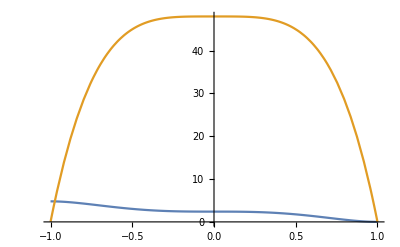

```mathematica
functionMUpdateSpherical[x_] = mUpdateSpherical /. {m->x, γ->0,Δ->.001};
functionPopRisk[x_] =PopRisk /.{m ->x,Δ->0.001}
EffectivePontentialSGD[m_]= -Integrate[functionMUpdateSpherical[x], {x,1,m}]
Plot[{EffectivePontentialSGD[m],functionPopRisk[m]},{m,-1,1}]
```

```mathematica
IsserlisTheorem[I4]
```

-162 ω[1,3] ω[1,4]+162 ω[1,3] ω[1,4] ω[2,2]+324 ω[1,2] ω[1,4] ω[2,3]-324 ω[1,3] ω[1,4] ω[2,3]^2+324 ω[1,2] ω[1,3] ω[2,4]-162 ω[2,3] ω[2,4]+162 ω[1,1] ω[2,3] ω[2,4]-324 ω[1,3]^2 ω[2,3] ω[2,4]-324 ω[1,4]^2 ω[2,3] ω[2,4]-324 ω[1,3] ω[1,4] ω[2,4]^2+162 ω[1,3] ω[1,4] ω[3,3]-162 ω[1,3] ω[1,4] ω[2,2] ω[3,3]-324 ω[1,2] ω[1,4] ω[2,3] ω[3,3]-324 ω[1,2] ω[1,3] ω[2,4] ω[3,3]+162 ω[2,3] ω[2,4] ω[3,3]-162 ω[1,1] ω[2,3] ω[2,4] ω[3,3]+324 ω[1,4]^2 ω[2,3] ω[2,4] ω[3,3]+324 ω[1,3] ω[1,4] ω[2,4]^2 ω[3,3]+81 ω[3,4]-81 ω[1,1] ω[3,4]+162 ω[1,2]^2 ω[3,4]+162 ω[1,3]^2 ω[3,4]+162 ω[1,4]^2 ω[3,4]-81 ω[2,2] ω[3,4]+81 ω[1,1] ω[2,2] ω[3,4]-162 ω[1,3]^2 ω[2,2] ω[3,4]-162 ω[1,4]^2 ω[2,2] ω[3,4]-648 ω[1,2] ω[1,3] ω[2,3] ω[3,4]+162 ω[2,3]^2 ω[3,4]-162 ω[1,1] ω[2,3]^2 ω[3,4]+324 ω[1,4]^2 ω[2,3]^2 ω[3,4]-648 ω[1,2] ω[1,4] ω[2,4] ω[3,4]+1296 ω[1,3] ω[1,4] ω[2,3] ω[2,4] ω[3,4]+162 ω[2,4]^2 ω[3,4]-162 ω[1,1] ω[2,4]^2 ω[3,4]+324 ω[1,3]^2 ω[2,4]^2 ω[3,4]-81 ω[3,3] ω[3,4]+81 ω[1,1] ω[3,3] ω[3,4]-162 ω[1,2]^2 ω[3,3] ω[3,4]-162 ω[1,4]^2 ω[3,3] ω[3,4]+81 ω[2,2] ω[3,3] ω[3,4]-81 ω[1,1] ω[2,2] ω[3,3] ω[3,4]+162 ω[1,4]^2 ω[2,2] ω[3,3] ω[3,4]+648 ω[1,2] ω[1,4] ω[2,4] ω[3,3] ω[3,4]-162 ω[2,4]^2 ω[3,3] ω[3,4]+162 ω[1,1] ω[2,4]^2 ω[3,3] ω[3,4]-324 ω[1,3] ω[1,4] ω[3,4]^2+324 ω[1,3] ω[1,4] ω[2,2] ω[3,4]^2+648 ω[1,2] ω[1,4] ω[2,3] ω[3,4]^2+648 ω[1,2] ω[1,3] ω[2,4] ω[3,4]^2-324 ω[2,3] ω[2,4] ω[3,4]^2+324 ω[1,1] ω[2,3] ω[2,4] ω[3,4]^2+54 ω[3,4]^3-54 ω[1,1] ω[3,4]^3+108 ω[1,2]^2 ω[3,4]^3-54 ω[2,2] ω[3,4]^3+54 ω[1,1] ω[2,2] ω[3,4]^3+162 ω[1,3] ω[1,4] ω[4,4]-162 ω[1,3] ω[1,4] ω[2,2] ω[4,4]-324 ω[1,2] ω[1,4] ω[2,3] ω[4,4]+324 ω[1,3] ω[1,4] ω[2,3]^2 ω[4,4]-324 ω[1,2] ω[1,3] ω[2,4] ω[4,4]+162 ω[2,3] ω[2,4] ω[4,4]-162 ω[1,1] ω[2,3] ω[2,4] ω[4,4]+324 ω[1,3]^2 ω[2,3] ω[2,4] ω[4,4]-162 ω[1,3] ω[1,4] ω[3,3] ω[4,4]+162 ω[1,3] ω[1,4] ω[2,2] ω[3,3] ω[4,4]+324 ω[1,2] ω[1,4] ω[2,3] ω[3,3] ω[4,4]+324 ω[1,2] ω[1,3] ω[2,4] ω[3,3] ω[4,4]-162 ω[2,3] ω[2,4] ω[3,3] ω[4,4]+162 ω[1,1] ω[2,3] ω[2,4] ω[3,3] ω[4,4]-81 ω[3,4] ω[4,4]+81 ω[1,1] ω[3,4] ω[4,4]-162 ω[1,2]^2 ω[3,4] ω[4,4]-162 ω[1,3]^2 ω[3,4] ω[4,4]+81 ω[2,2] ω[3,4] ω[4,4]-81 ω[1,1] ω[2,2] ω[3,4] ω[4,4]+162 ω[1,3]^2 ω[2,2] ω[3,4] ω[4,4]+648 ω[1,2] ω[1,3] ω[2,3] ω[3,4] ω[4,4]-162 ω[2,3]^2 ω[3,4] ω[4,4]+162 ω[1,1] ω[2,3]^2 ω[3,4] ω[4,4]+81 ω[3,3] ω[3,4] ω[4,4]-81 ω[1,1] ω[3,3] ω[3,4] ω[4,4]+162 ω[1,2]^2 ω[3,3] ω[3,4] ω[4,4]-81 ω[2,2] ω[3,3] ω[3,4] ω[4,4]+81 ω[1,1] ω[2,2] ω[3,3] ω[3,4] ω[4,4]

```mathematica
FortranForm[IsserlisTheorem[I2noise]/.{ω->c}]
```

9 - 9*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,1) + 18*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -       135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,2)**2 - 9*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,2) + 9*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(2,2)

```mathematica
FortranForm[IsserlisTheorem[I2]/.{ω->c}]
```

9 - 18*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,1) + 9*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -       135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,1)**2 + 72*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -       4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,2)**2 - 
     -  72*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -       270*q*ρ**3 + 405*q**2*ρ**3)(1,2)**2 + 24*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -       486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,2)**4 - 18*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,2) + 36*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(2,2) - 18*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -       486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,1)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,2) - 72*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -       405*q**2*ρ**3)(1,2)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,2) + 72*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -       4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,2)**2*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(2,2) + 9*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -       135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,2)**2 - 18*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -       324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,2)**2 + 
     -  9*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -       405*q**2*ρ**3)(1,1)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -       135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,2)**2

```mathematica
FortranForm[IsserlisTheorem[I3]/.{ω->c}]
```

-18*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(1,3) + 9*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,3) - 9*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,3) + 
     -  18*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -       405*q**2*ρ**3)(1,3)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,3) + 18*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3) - 
     -  9*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(2,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(3,3) + 9*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3)

```mathematica
FortranForm[IsserlisTheorem[I4]/.{ω->c}]
```

-162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(1,4) + 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,2) + 
     -  324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,3) - 324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -       324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,3)**2 + 
     -  324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4) - 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4) + 162*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(2,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4) - 324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -       486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4) - 
     -  324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -       405*q**2*ρ**3)(1,4)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4) - 324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -       405*q**2*ρ**3)(2,4)**2 + 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3) - 162*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3) - 324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(2,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(3,3) - 324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4)*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(3,3) + 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3) - 162*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(2,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3) + 324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -       4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)**2*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(2,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(2,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3) + 324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -       324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4)**2*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(3,3) + 81*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) - 81*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) + 162*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -       405*q**2*ρ**3)(1,2)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) + 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -       486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) + 162*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -       405*q**2*ρ**3)(1,4)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) - 81*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) + 81*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(2,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) - 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -       486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) - 
     -  162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -       405*q**2*ρ**3)(1,4)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) - 648*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(2,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(3,4) + 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -       486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,3)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) - 162*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -       270*q*ρ**3 + 405*q**2*ρ**3)(2,3)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) + 324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -       4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)**2*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -       405*q**2*ρ**3)(2,3)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) - 648*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4)*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(3,4) + 1296*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4)*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(3,4) + 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -       135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) - 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -       324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4)**2*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(3,4) + 324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -       135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -       486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) - 81*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(3,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(3,4) + 81*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) - 
     -  162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -       405*q**2*ρ**3)(1,2)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) - 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -       4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)**2*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(3,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(3,4) + 81*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) - 
     -  81*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(2,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) + 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -       4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)**2*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(2,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(3,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) + 648*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4)*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(3,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(3,4) - 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -       486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) + 
     -  162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -       270*q*ρ**3 + 405*q**2*ρ**3)(2,4)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4) - 324*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -       135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4)**2 + 324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(2,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -       270*q*ρ**3 + 405*q**2*ρ**3)(3,4)**2 + 648*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,3)*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -       405*q**2*ρ**3)(3,4)**2 + 648*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -       324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4)**2 - 
     -  324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(2,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(2,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -       135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4)**2 + 324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,3)*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(2,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -       270*q*ρ**3 + 405*q**2*ρ**3)(3,4)**2 + 54*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -       486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4)**3 - 54*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -       324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4)**3 + 
     -  108*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -       405*q**2*ρ**3)(1,2)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -       135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4)**3 - 54*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -       324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4)**3 + 
     -  54*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(2,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -       135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4)**3 + 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(4,4) - 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(4,4) - 
     -  324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(4,4) + 324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -       405*q**2*ρ**3)(2,3)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(4,4) - 324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4)*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(4,4) + 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(4,4) - 162*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(2,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(4,4) + 324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -       4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)**2*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(2,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(2,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(4,4) - 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3)*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(4,4) + 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3)*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(4,4) + 324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3)*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(4,4) + 324*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3)*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(4,4) - 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(4,4) + 
     -  162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(2,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(4,4) - 81*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(3,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(4,4) + 81*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(4,4) - 
     -  162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -       405*q**2*ρ**3)(1,2)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(4,4) - 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -       4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)**2*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(3,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(4,4) + 81*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(4,4) - 
     -  81*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(2,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(4,4) + 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -       4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)**2*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(2,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(3,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(4,4) + 648*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,3)*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(3,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(4,4) - 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -       486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,3)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(4,4) + 
     -  162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -       270*q*ρ**3 + 405*q**2*ρ**3)(2,3)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(4,4) + 81*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(3,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(3,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(4,4) - 81*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4)*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(4,4) + 162*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -       135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,2)**2*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(4,4) - 
     -  81*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(2,2)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(3,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(3,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 
     -      486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(4,4) + 81*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 
     -      4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(1,1)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 
     -      324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(2,2)*
     -   (-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 270*q*ρ**3 + 
     -      405*q**2*ρ**3)(3,3)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 135*ρ**3 - 
     -      270*q*ρ**3 + 405*q**2*ρ**3)(3,4)*(-324*m**2 - 1296*m**4 + 972*m**2*q + 81*ρ + 1296*m**2*ρ + 3240*m**4*ρ - 162*q*ρ - 3888*m**2*q*ρ + 243*q**2*ρ - 162*ρ**2 - 1620*m**2*ρ**2 + 324*q*ρ**2 + 4860*m**2*q*ρ**2 - 486*q**2*ρ**2 + 
     -      135*ρ**3 - 270*q*ρ**3 + 405*q**2*ρ**3)(4,4)